```mathematica
kEC = 1.60217733 10^-19
kAMC = 1.660538921 10^-27
kC=N[(2 kEC)/kAMC]
A[m_,V_]:=(V kEC)/(m kAMC);       (* V := accelerator voltage, m := mass *)
acceleratorVoltage[ t_, length_, m_ ] := length^2 m / (t^2 kC)
```

1.60218×10^-19

1.66054×10^-27

1.92971×10^8

```mathematica
d = { 0.06626, 0.30512, 0.66273,  0.0 };
L[n_] := d[[3]]  n               (* Compute length (m) at n-laps *)
fLength[n_]:=d[[1]] + d[[1]] + d[[2]] + d[[4]] + n  d[[3]]  (*length with injection+ejection*)
sLength[n_] := d[[1]] + d[[1]] + d[[2]] + n  d[[3]]
```

```mathematica
T[m_,V_,L_]:=(L √m)/(√V √kC);
```

```mathematica
Solve[(l* √m)/(√v √kC) == t,m]
```

{{m→(0.0830735 v)/l^2}}

```mathematica
t2m[t_,V_,l_]:=(kC t^2 V)/l^2
```

```mathematica
mAr = 39.96183454;
mMe = 16.03075155;
mN2 = 28.00559943;
mXe = 131.9036049;
```

```mathematica
Me = {{6.3371784 10^-05,20},{9.9921119 10^-05,32},{1.5474489 10^-04,50}};
N2 ={{8.3684315 10^-05,20},{1.2393971 10^-04,30}};
Ar = { {9.9916768 10^-5, 20},{1.4800454 10^-4,  30 }};
Xe = { {1.8133327 10^-04, 20},{2.6869789 10^-04, 30},{4.4342763 10^-04, 50}  };
M = { Me,N2,Ar,Xe};
masses = {mMe, mN2,mAr,mXe};
```

```mathematica
(*mm[[mass]][[ [tof,lap],[tof,lap] ]]*)
MM = {{ mMe,{{6.3371784 10^-05,20},{9.9921119 10^-05,32}}}
,{mMe, {{9.9921119 10^-05,32},{1.5474489 10^-04,50}}}
,{mN2,{{8.3684315 10^-05,20},{1.2393971 10^-04,30}}}
,{mAr,{{9.9916768 10^-5, 20},{1.4800454 10^-4,  30 }}}
,{mXe,{{1.8133327 10^-04, 20},{2.6869789 10^-04, 30}}}
,{mXe,{{2.6869789 10^-04, 30},{4.4342763 10^-04, 50}}}
};
MTOF = {{ mMe,{6.3371784 10^-05,20}}
,{mMe, {9.9921119 10^-05,32}}
,{mMe,{1.5474489 10^-04,50}}
,{mN2,{8.3684315 10^-05,20}}
,{mN2,{1.2393971 10^-04,30}}
,{mAr,{9.9916768 10^-5, 20}}
,{mAr,{1.4800454 10^-4,  30 }}
,{mXe,{1.8133327 10^-04, 20}}
,{mXe,{2.6869789 10^-04, 30}}
,{mXe,{4.4342763 10^-04, 50}}
};
```

```mathematica
fVelocity[dlap_] := d[[3]]/(dlap[[1]]/dlap[[2]])
tlap[mat_] := mat[[1]]/mat[[2]];                                       (*lap-time*)
tHalfCycle[a_,b_] := b[[1]]-tlap[b-a]*b[[2]]  (* flight-time for half-cycle part *)
lHalfCycle[mm_]         := tHalfCycle[mm[[2,2]],mm[[2,1]]] * fVelocity[mm[[2,2]]-mm[[2,1]]];
halfCycleTime[mm_] := mm[[2,2]][[1]]-tlap[mm[[2,2]]-mm[[2,1]]]*mm[[2,2]][[2]];
```

#### Accelerator voltage estimation

```mathematica
hmode = ConstantArray[{0,0,0},Length[MM]]; (*time,length,mass for half-cycle mode*)
Do[  hmode[[i]] = {halfCycleTime[MM[[i]]],lHalfCycle[MM[[i]]],MM[[i]][[1]] }, {i,Length[MM]}]
```

```mathematica
hVa = ConstantArray[{0,0},Length[MM] ]; (* Va calculated from half-cycle mode *)
Do[ hVa[[i]] = { Sqrt[hmode[[i]][[3]]],acceleratorVoltage @@ hmode[[i]]},{i,Length[hmode]}]
```

### TOF Equation (scan law) on orbital period

```mathematica
dMM = ConstantArray[ {0,0},Length[MM] ];
Do [ dMM[[i]] = MM[[All,2]][[i]][[2]]-MM[[All,2]][[i]][[1]] , {i,Length[MM]}]
```

FittedModel[6.32768×10^-10+1.14781×10^-6 x]

{6.32768×10^-10,1.14781×10^-6}

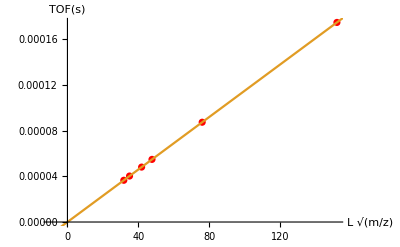

```mathematica
tlaps = Transpose[{ Sqrt[MM[[All,1]]] * L[dMM[[All,2]]],dMM[[All,1]] }];
m0 = LinearModelFit[tlaps, x, x]
{offset0,slope0}=CoefficientList[ Normal[m0],x]
Show[ListPlot[tlaps, PlotStyle -> Red,PlotRange->{{-10,All},Full}]
      ,Plot[{line, m0[x]},{x,-100,400}]
      ,AxesLabel->{L Sqrt[m/z],"TOF(s)"}]
```

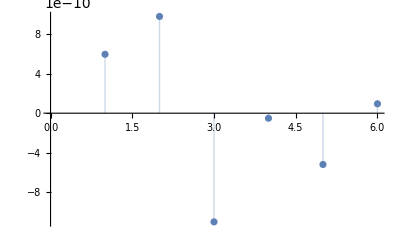

```mathematica
ListPlot[m0["FitResiduals"], Filling -> Axis]
```

```mathematica
Va = acceleratorVoltage[slope0 ,1,1] (* mass = 1, length = 1m*)
```

3933.4

```mathematica
fx[x_] :=offset0 + slope0 * x
m0[(Sqrt[MM[[1,1]]] * L[ dMM[[1,2]] ])]-fx[Sqrt[mMe] * L[12]]; (*validation*)
```

```mathematica
Clear[x,t];
Solve[offs + slope x == t, x];
invfx[t_] := (-offset0 + t)/slope0
```

```mathematica
invfx[dMM[[All,1]]]/Sqrt[MM[[All,1]]]/L[1] (*validation; time -> lap number *)
```

{12.0002,18.0003,9.99973,9.99999,9.99994,20.}

### Compensation length calculation

FittedModel[2.28581×10^-7+5.16335×10^-8 x]

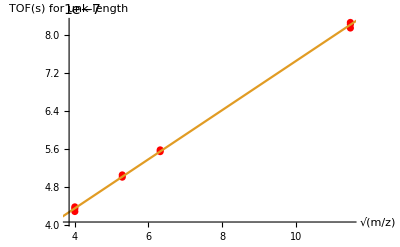

{2.28581×10^-7,5.16335×10^-8}

0.0449595

```mathematica
tof = MTOF[[All,2,1]];
lap = MTOF[[All,2,2]];
uTOF = Transpose[{Sqrt[MTOF[[All, 1]]],(tof  - (fx[Sqrt[MTOF[[All, 1]]]])*sLength[lap] )}];
pu = LinearModelFit[uTOF, x,x]
Show[ListPlot[uTOF, PlotStyle -> Red, PlotRange -> {All, All}]
       , Plot[{line, pu[x]}, {x, 0, 12}], AxesLabel -> {Sqrt[m/z], "TOF(s) for unk-length"}]
uEq = CoefficientList[Normal[pu], x]
d[[4]]  =uEq[[2]]/ fx[1]
```

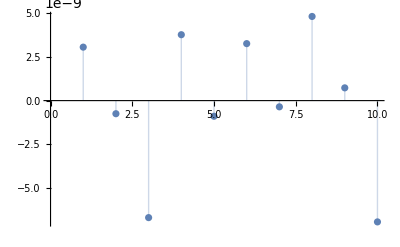

```mathematica
ListPlot[pu["FitResiduals"], Filling -> Axis]
```

### Estimate scan-law (the method where the QtPlatz used)

See infitof/src/libs/infwidgets/mspeakwidget.cpp, estimateScanLaw method

```mathematica
Clear[tof,length,mass,qt];
tof =  MTOF[[All,2,1]];
nlap = MTOF[[All,2,2]];
mass = MTOF[[All,1]] ;
qt=Transpose[{Sqrt[mass] *fLength[nlap],tof}];
```

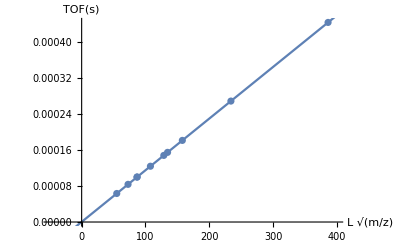

2.40582×10^-7

3933.35

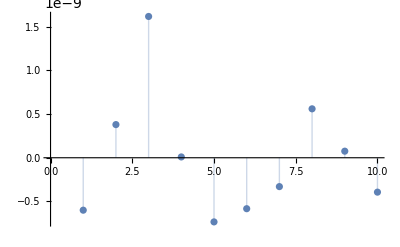

```mathematica
m1 =LinearModelFit[qt,x,x];
Show [ ListPlot[qt,PlotRange->{{-50,400},Full},AxesLabel->{L Sqrt[m/z],"TOF(s)"}]
, Plot[m1[x],{x,-50,400}]]
t0 = m1[0]
Vacc = acceleratorVoltage[m1[1]-m1[0],1,1] (* mass = 1, length = 1m*)
ListPlot[m1["FitResiduals"], Filling -> Axis]
```

#### // End Scan law Estimation

### Mass errors

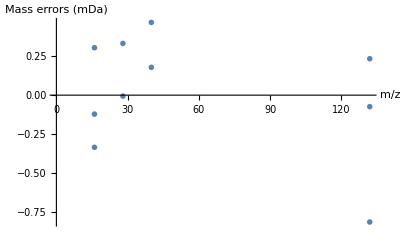

```mathematica
dm = (mass - t2m[tof-t0,Vacc,fLength[nlap]])*1000;
ListPlot[Transpose[{mass,dm}],PlotRange->{{0,All},All}
  , PlotMarkers->"OpenMarkers" 
, Filling->Axes
,AxesLabel->{m/z,"Mass errors (mDa)"}]
```

### Estimate scan law (by argon)

```mathematica
tof2 = Ar[[All,1]];
lap2 = Ar[[All,2]];
mass2 = ConstantArray[ mAr, Length[Ar]];
pm2=LinearModelFit[Transpose[{Sqrt[mass2] *fLength[lap2],tof2}],x, x];
{t02,slope2}=CoefficientList[Normal[pm2],x];
Vacc2 = acceleratorVoltage[slope2,1,1] (* mass = 1, length = 1m*)
```

3933.31

#### Mass errors (for argon ion based scan law)

```mathematica
dm2 = mass - t2m[ tof - t02, Vacc2, fLength[lap]];
```

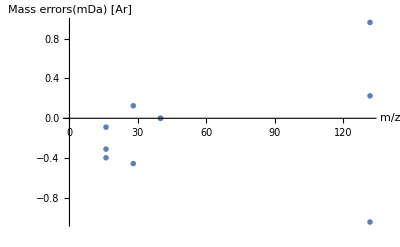

```mathematica
ListPlot[Transpose[{mass,dm2*1000}],PlotRange->{{0,All},All}
,PlotMarkers->"OpenMarkers", AxesLabel->{m/z,"Mass errors(mDa) [Ar]"}]
```

### Estimate scan law by using methane ion

```mathematica
{tof3,lap3,mass3} = {Me[[All,1]],Me[[All,2]],ConstantArray[mMe,Length[Me]]};
pm3=LinearModelFit[ Transpose[{Sqrt[mass3] *fLength[lap3],tof3}],x, x];
{t03,slope3}=CoefficientList[Normal[pm3],x];
Vacc3 = acceleratorVoltage[slope3,1,1] (* mass = 1, length = 1m*)
```

3933.16

#### Mass errors (methane)

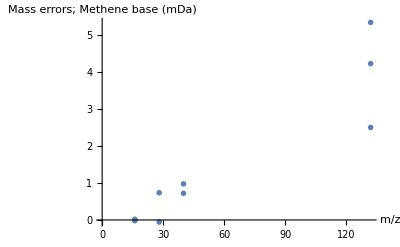

```mathematica
dm3 = (mass - t2m[tof-t03,Vacc3,fLength[lap]])*1000;
ListPlot[Transpose[{mass,dm3}],PlotRange->{{0,All},All}
,PlotMarkers->"OpenMarkers", AxesLabel->{m/z,"Mass errors; Methene base (mDa)"}]
```

### Estimate scan law by using xenon ion

```mathematica
{tof4,lap4,mass4} = {Xe[[All,1]],Xe[[All,2]],ConstantArray[mXe,Length[Xe]]};
pm4=LinearModelFit[ Transpose[{Sqrt[mass4] *fLength[lap4],tof4}],x, x];
{t04,slope4}=CoefficientList[Normal[pm4],x];
Vacc4 = acceleratorVoltage[slope4,1,1] (* mass = 1, length = 1m*)
```

3933.38

#### Mass errors (for xenon ion based scan law)

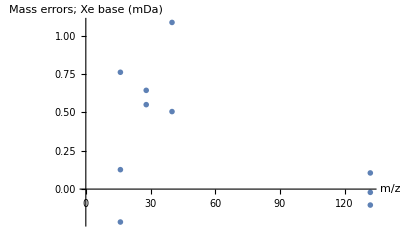

```mathematica
dm4 = (mass - t2m[tof-t04,Vacc4,fLength[lap]])*1000;
ListPlot[Transpose[{mass,dm4}],PlotRange->{{0,All},All}
,PlotMarkers->"OpenMarkers", AxesLabel->{m/z,"Mass errors; Xe base (mDa)"}]
```

# Constant accelerated equation of motion

```mathematica
S[a_,t_,v_]:=v t+(a t^2)/2
```

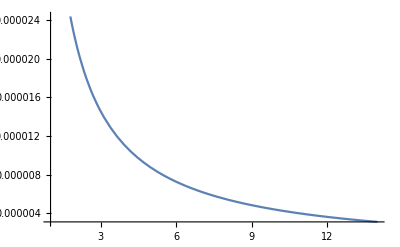

```mathematica
(*flight distance for 50ps at various m/z *)
Plot[S[A[q^2,5000],50 10^-12,1/T[q^2,Va,1]],{q,1,14}]
```

```mathematica
Clear[v,t,a,s]
Solve[v t + (a t^2)/2 ==s,t]
```

{{t→(-v-√(2 a s+v^2))/a},{t→(-v+√(2 a s+v^2))/a}}

```mathematica
Solve[v t + (a t^2)/2 ==s,t]
```

{{t→(-v-√(2 a s+v^2))/a},{t→(-v+√(2 a s+v^2))/a}}

```mathematica
caTOF[a_,L_,v_]:=(-v+√(2 a L+v^2))/a
fv[a_,t_,v_] := v + a t
```

```mathematica
caTOF[A[q^2,5000],0.004,1/T[q^2,Va,1]]/.q->Sqrt[132]
caTOF[A[q^2,-5000],0.004,1/T[q^2,Va,1]]/.q->Sqrt[132]
```

5.26825×10^-8

5.28166×10^-8

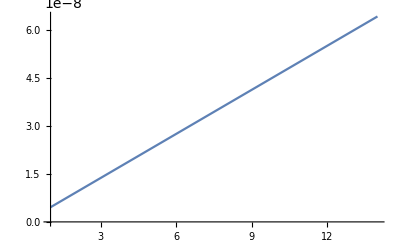

```mathematica
Plot[caTOF[A[q^2,-5000],0.004,1/T[q^2,Va,1]],{q,1,14}]
```

```mathematica
t=(1/T[132,Va,1])/A[132,5000]
```

0.0000207484

```mathematica
(1/2) A[132,Va] t^2
```

0.618866

75830.3

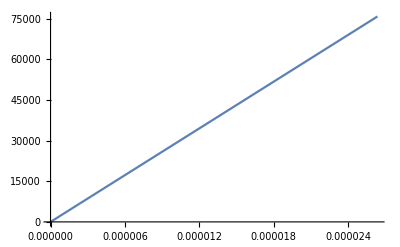

```mathematica
1/T[132,Va,1]
Plot[fv[A[132,Va],t,0],{t,0,26.375 10^-6}]
```

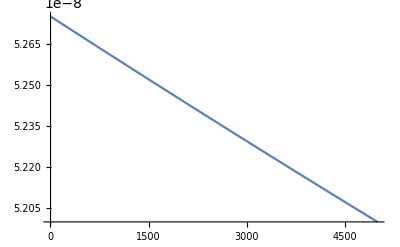

```mathematica
Plot[caTOF[A[Sqrt[132],V],0.004,1/T[132,Va,1]],{V,1,5000}]
```

```mathematica
xTof = Transpose[{mass,tof-T[mass,Va,length]}]
```

{{16.0308,0.0000633718-4.59565×10^-6 length},{16.0308,0.0000999211-4.59565×10^-6 length},{16.0308,0.000154745-4.59565×10^-6 length},{28.0056,0.0000836843-6.07425×10^-6 length},{28.0056,0.00012394-6.07425×10^-6 length},{39.9618,0.0000999168-7.25592×10^-6 length},{39.9618,0.000148005-7.25592×10^-6 length},{131.904,0.000181333-0.0000131825 length},{131.904,0.000268698-0.0000131825 length},{131.904,0.000443428-0.0000131825 length}}

```mathematica
tplot = Fit[xTof,{1,m},m];
coef = CoefficientList[tplot,m]
Show[ListPlot[xTof, PlotStyle -> Red,PlotRange->{{0,140},All}]
      ,Plot[{line, tplot},{m,0,140}]
      ,AxesLabel->{m/z,"ΔTOF(s)"}]
```

{0.316228 (-0.245702 (0.000181333-0.0000131825 length)-0.245702 (0.000268698-0.0000131825 length)-0.245702 (0.000443428-0.0000131825 length)+0.453134 (0.0000999168-7.25592×10^-6 length)+0.453134 (0.000148005-7.25592×10^-6 length)+0.544012 (0.0000836843-6.07425×10^-6 length)+0.544012 (0.00012394-6.07425×10^-6 length)+0.635031 (0.0000633718-4.59565×10^-6 length)+0.635031 (0.0000999211-4.59565×10^-6 length)+0.635031 (0.000154745-4.59565×10^-6 length)),0.004162 (0.736458 (0.000181333-0.0000131825 length)+0.736458 (0.000268698-0.0000131825 length)+0.736458 (0.000443428-0.0000131825 length)-0.179428 (0.0000999168-7.25592×10^-6 length)-0.179428 (0.000148005-7.25592×10^-6 length)-0.298531 (0.0000836843-6.07425×10^-6 length)-0.298531 (0.00012394-6.07425×10^-6 length)-0.417819 (0.0000633718-4.59565×10^-6 length)-0.417819 (0.0000999211-4.59565×10^-6 length)-0.417819 (0.000154745-4.59565×10^-6 length))}

-Graphics-

```mathematica
Show[
Plot[coef[[1]]+caTOF[A[m,5000],0.0005,1/T[m,Va,1]],{m,1,140},PlotRange->{All,All}]
,Plot[coef[[1]]+coef[[2]]*m +caTOF[A[m,-5000],0.004,1/T[m,Va,1]],{m,1,140}, PlotStyle->Cyan]
,Plot[coef[[1]]+coef[[2]]*m ,{m,1,140},PlotStyle->Red]
,ListPlot[xTof, PlotStyle -> Red]
   ,AxesLabel->{m/z,"ΔTOF(s)"}]
A[m,1000]-A[m,5000]/.m->132
```

-Graphics-

-2.9238×10^9

```mathematica
T[m,Va,L]/.{m->132,L->0.004} 
caTOF[A[m,5000],L,(1/T[m,Va,1])]/.{m->132,L->0.004}
 T[m,Va,L]-caTOF[A[m,V2],L,(1/T[m,Va,1])] /.{m->132,L->0.004,V2->5000}
```

5.27493×10^-8

5.26825×10^-8

6.68831×10^-11

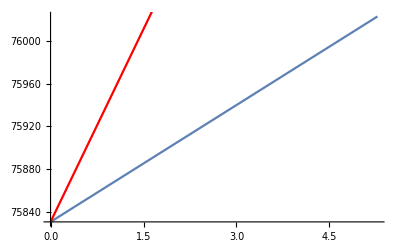

```mathematica
Show[
Plot[A[m,5000]*t + 1/T[m,Va,1]/.m->132, {t,0,T[132,Va,0.004]}]
,Plot[A[m,5000]*t + 1/T[132,Va,1]/.m->40, {t,0,T[132,Va,0.004]},PlotStyle->Red]
]
```

```mathematica
caTOF[A[m,1000],L,(1/T[m,Va,1])] - caTOF[A[m,V2],L,(1/T[m,Va,1])] /.{m->132,L->0.004,V2->5000}
```

5.34793×10^-11

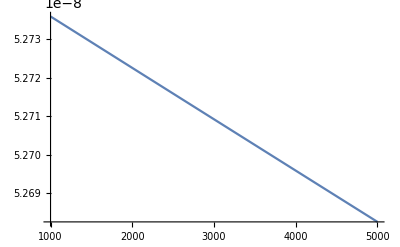

```mathematica
Show[
Plot[caTOF[A[m,V2],L,(1/T[m,Va,1])] /.{m->132,L->0.004}, {V2,1000,5000}]
]
```